```mathematica
β[ω_,δ_,t_,ϵ_,m_]:=β[ω,δ,t,ϵ,m]=ReplacePart[(ω+ⅈ*δ-ϵ)IdentityMatrix[m],Join[Table[{i,i-1},{i,Range[2,m,1]}],Table[{i,i+1},{i,Range[1,m,1]}]]->-t]
```

```mathematica
T[t_,m_]:=T[t,m]=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=t*IdentityMatrix[m];MAT]
```

```mathematica
Clear[leads]
```

```mathematica
leads[y_]:=leads[y]=Table[ToExpression[Import["~/Downloads/PhD_new/PhD/fwi/sq_lattice/leads/size_"<>ToString[y]<>"_lead_"<>ToString[x]<>"_.dat"]],{x,Range[0,2.49,0.01]}]
```

```mathematica
leads[10]
```

```mathematica
LEFT[ω_,m_]:=LEFT[ω,m]=leads[m][[Round[ω*100+1]]]
```

```mathematica
Clear[dist,list]
```

```mathematica
list[upleft_,downleft_,upright_,downright_]:=Module[{},Join[Transpose[Join[{Range[1,25]},{RandomSample[Join[Table[RandomInteger[{1,12}],upleft],Table[RandomInteger[{13,25}],downleft],Table[RandomInteger[{26,50}],5]]]}]],Transpose[Join[{Range[26,50]},{RandomSample[Join[Table[RandomInteger[{1,12}],upright],Table[RandomInteger[{13,25}],downright],Table[RandomInteger[{26,50}],5]]]}]]]]
```

```mathematica
dist[diagonal_]:=dist[diagonal]=Table[Module[{x=RandomInteger[{1,diagonal}]},list[x,20-x,20-(diagonal-x),diagonal-x]],5000]
```

```mathematica
dist[20][[1]]
```

```mathematica
TLD[t_]:=Module[{sizeoflead=10},Module[{mat=RandomInteger[0,{50,50}]},ReplacePart[mat,Table[{a,a},{a,11,20}]->t]]]
```

```mathematica
g[ω_,δ_,t_,ϵ_]:= Inverse[β[ω,δ,t,ϵ,50]]
```

```mathematica
Clear[SLLEAD]
```

```mathematica
SLLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[1;;m,1;;m]]=LEFT[ω,m];MAT]
```

```mathematica
SRLEAD[ω_,m_]:=Module[{MAT=0*IdentityMatrix[50]},MAT[[11;;20,11;;20]]=LEFT[ω,m];MAT]
```

```mathematica
device1[ω_]:=Module[{sizeoflead=10},Inverse[IdentityMatrix[50]-g[ω,0.0001,1,0].T[1,sizeoflead].SLLEAD[ω,sizeoflead].T[1,sizeoflead]].g[ω,0.0001,1,0]]
```

```mathematica
device1[1][[1,1]]
```

0.376543-0.675031 ⅈ

```mathematica
ListLinePlot[Table[{ω,-Im[device1[ω][[10,10]]]},{ω,Range[0,2.4,0.01]}]]
```

```mathematica
dist[20][[1]]
```

{{1,16},{2,20},{3,18},{4,19},{5,37},{6,22},{7,15},{8,19},{9,17},{10,17},{11,5},{12,14},{13,16},{14,25},{15,44},{16,27},{17,21},{18,19},{19,15},{20,16},{21,15},{22,44},{23,22},{24,28},{25,25},{26,14},{27,16},{28,35},{29,16},{30,21},{31,18},{32,13},{33,10},{34,15},{35,17},{36,30},{37,14},{38,30},{39,24},{40,15},{41,18},{42,41},{43,21},{44,15},{45,47},{46,18},{47,23},{48,19},{49,15},{50,14}}

```mathematica
TLD[1]
```

```mathematica
CA[ω_,ϵ1_,diagonal_,number_]:= Module[{sizeoflead=10},
recurs=Module[{J= device1[ω]},
Do[
J=Inverse[IdentityMatrix[50]-Inverse[Module[{κ=β[ω,0.0001,1,0,50],n= dist[diagonal][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]].T[1,50].J.T[1,50]].Inverse[Module[{κ=β[ω,0.0001,1,0,50],n= dist[diagonal][[number]][[loc1,2]]},ReplacePart[κ,{{n,n}}->ω+ⅈ*0.0001-ϵ1]]],{loc1,50}];J=J];ir=Inverse[IdentityMatrix[50]-SRLEAD[ω,sizeoflead].TLD[1].recurs.TLD[1]].SRLEAD[ω,sizeoflead];il=Inverse[IdentityMatrix[50]-recurs.TLD[1].SRLEAD[ω,sizeoflead].TLD[1]].recurs;
gdd1= il-ConjugateTranspose[il];
grr1= ir-ConjugateTranspose[ir];
Gnonlocalrl=ir.TLD[1].recurs;
(*Gnonlocallr=recurs.ConjugateTranspose[TLD[1]].ir;*)
GNON1= Gnonlocalrl-ConjugateTranspose[Gnonlocalrl];TRA=Abs[Tr[gdd1.TLD[1].grr1.TLD[1]-TLD[1].GNON1.TLD[1].GNON1]];TRA]
```

```mathematica
CA[1,1,12,1]
```

2.80849

```mathematica
ListLinePlot[Table[{ω,Print[ω];CA[ω,0,10,1]},{ω,Range[0,2,0.01]}]]
```

```mathematica
input=Table[Print[num];ParallelTable[{ω,CA[ω,1,12,num]},{ω,Range[0,2,0.01]}],{num,10}]
```

{{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},{0.15,0.330437},{0.16,0.416412},{0.17,1.11097},{0.18,1.46869},{0.19,1.04827},{0.2,1.922},{0.21,0.372763},{0.22,1.68871},{0.23,0.629716},{0.24,0.458776},{0.25,1.36573},{0.26,0.58685},{0.27,1.98066},{0.28,1.08329},{0.29,1.25332},{0.3,0.498546},{0.31,0.0683238},{0.32,6.9347},{0.33,4.30767},{0.34,0.608195},{0.35,0.973414},{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},{0.5,2.3191},{0.51,3.03397},{0.52,2.32388},{0.53,2.44577},{0.54,1.46628},{0.55,2.56677},{0.56,1.96303},{0.57,1.69895},{0.58,1.94833},{0.59,2.07016},{0.6,1.66796},{0.61,2.10013},{0.62,2.3548},{0.63,1.87031},{0.64,2.10503},{0.65,1.38228},{0.66,1.40287},{0.67,1.60955},{0.68,0.135591},{0.69,0.380592},{0.7,1.5159},{0.71,2.55363},{0.72,1.79824},{0.73,1.00296},{0.74,1.81511},{0.75,0.260269},{0.76,2.43524},{0.77,1.36891},{0.78,1.94291},{0.79,2.16571},{0.8,1.38958},{0.81,2.33358},{0.82,2.77945},{0.83,2.58139},{0.84,2.79841},{0.85,2.4333},{0.86,3.24146},{0.87,3.20493},{0.88,2.89522},{0.89,2.79101},{0.9,1.17667},{0.91,2.91656},{0.92,2.78164},{0.93,2.84991},{0.94,2.0565},{0.95,2.26405},{0.96,3.0585},{0.97,2.63105},{0.98,2.89126},{0.99,2.89433},{1.,2.80849},{1.01,2.30805},{1.02,2.20643},{1.03,1.28374},{1.04,2.0589},{1.05,2.31084},{1.06,2.03273},{1.07,2.02704},{1.08,2.62024},{1.09,2.47862},{1.1,2.72496},{1.11,2.61923},{1.12,2.19},{1.13,1.86129},{1.14,1.6608},{1.15,2.18165},{1.16,2.05637},{1.17,2.84815},{1.18,2.93461},{1.19,0.735755},{1.2,2.30511},{1.21,1.22723},{1.22,0.717838},{1.23,0.452703},{1.24,0.890053},{1.25,1.60871},{1.26,2.30315},{1.27,1.36636},{1.28,1.75141},{1.29,2.26421},{1.3,1.57321},{1.31,2.32665},{1.32,2.27872},{1.33,2.15634},{1.34,2.17732},{1.35,2.07261},{1.36,2.76452},{1.37,3.23237},{1.38,2.60324},{1.39,1.70981},{1.4,2.78485},{1.41,2.2634},{1.42,2.19082},{1.43,2.31171},{1.44,1.83556},{1.45,2.11873},{1.46,3.02743},{1.47,2.90577},{1.48,2.49015},{1.49,2.83243},{1.5,2.05901},{1.51,2.18005},{1.52,2.11207},{1.53,2.88147},{1.54,2.76428},{1.55,2.06604},{1.56,1.73273},{1.57,2.10961},{1.58,2.60403},{1.59,2.62053},{1.6,2.81644},{1.61,1.90604},{1.62,2.99902},{1.63,2.64858},{1.64,2.57487},{1.65,2.16599},{1.66,1.11148},{1.67,1.77667},{1.68,1.2679},{1.69,1.76038},{1.7,1.82175},{1.71,2.07517},{1.72,2.11542},{1.73,2.02464},{1.74,1.50615},{1.75,0.868105},{1.76,1.43695},{1.77,2.05143},{1.78,1.50607},{1.79,0.557057},{1.8,2.14772},{1.81,2.25657},{1.82,2.10979},{1.83,2.64666},{1.84,1.62379},{1.85,2.03837},{1.86,2.59823},{1.87,0.103608},{1.88,1.55601},{1.89,2.10437},{1.9,2.21167},{1.91,1.99954},{1.92,2.62251},{1.93,1.74779},{1.94,2.18934},{1.95,2.42439},{1.96,2.05611},{1.97,2.01015},{1.98,2.35724},{1.99,1.99913},{2.,1.83553}},{{0.,3.77872},{0.01,1.88544},{0.02,2.9321},{0.03,0.00091111},{0.04,2.2164},{0.05,4.31439},{0.06,4.28749},{0.07,4.60508},{0.08,11.9906},{0.09,11.6865},{0.1,4.94672},{0.11,0.669099},{0.12,0.296234},{0.13,0.760015},{0.14,2.16816},{0.15,0.577615},{0.16,0.334279},{0.17,0.24369},{0.18,0.114922},{0.19,0.717367},{0.2,1.765},{0.21,1.30641},{0.22,0.195951},{0.23,0.977363},{0.24,0.291607},{0.25,0.46475},{0.26,0.225421},{0.27,0.722748},{0.28,0.158173},{0.29,0.127542},{0.3,0.670258},{0.31,5.11637},{0.32,1.6292},{0.33,0.374698},{0.34,0.909901},{0.35,0.897869},{0.36,2.2155},{0.37,0.387189},{0.38,0.412249},{0.39,0.222637},{0.4,1.51534},{0.41,0.798314},{0.42,1.19519},{0.43,0.432936},{0.44,0.018777},{0.45,1.3193},{0.46,2.27414},{0.47,1.90917},{0.48,1.83695},{0.49,1.93327},{0.5,1.72186},{0.51,1.59321},{0.52,2.11983},{0.53,1.19983},{0.54,2.26803},{0.55,1.1024},{0.56,1.92148},{0.57,2.20866},{0.58,1.4934},{0.59,2.74335},{0.6,1.77015},{0.61,1.48537},{0.62,2.73605},{0.63,1.41466},{0.64,2.31568},{0.65,1.52391},{0.66,0.0417012},{0.67,0.213216},{0.68,0.0518195},{0.69,1.34587},{0.7,0.60051},{0.71,0.443263},{0.72,0.135894},{0.73,0.832213},{0.74,1.26811},{0.75,1.08356},{0.76,0.748309},{0.77,2.10154},{0.78,1.78308},{0.79,0.641351},{0.8,1.44436},{0.81,1.30574},{0.82,2.15982},{0.83,1.5004},{0.84,1.36591},{0.85,2.32122},{0.86,2.43985},{0.87,1.86724},{0.88,2.86065},{0.89,2.23281},{0.9,2.28488},{0.91,2.2638},{0.92,1.9766},{0.93,1.62696},{0.94,1.26934},{0.95,1.92932},{0.96,2.00653},{0.97,1.91476},{0.98,1.85875},{0.99,2.39726},{1.,2.1478},{1.01,2.80025},{1.02,2.3263},{1.03,2.52529},{1.04,1.84211},{1.05,2.08276},{1.06,2.305},{1.07,2.25083},{1.08,2.719},{1.09,2.42188},{1.1,1.81469},{1.11,1.54026},{1.12,1.36943},{1.13,1.55927},{1.14,1.98155},{1.15,1.86293},{1.16,1.05511},{1.17,0.283121},{1.18,0.0800043},{1.19,1.15354},{1.2,1.92153},{1.21,1.50547},{1.22,0.997487},{1.23,1.96322},{1.24,1.91943},{1.25,1.32229},{1.26,0.687121},{1.27,1.73206},{1.28,1.94699},{1.29,1.65566},{1.3,1.95517},{1.31,1.86692},{1.32,2.52419},{1.33,2.47523},{1.34,2.38977},{1.35,1.87176},{1.36,1.7749},{1.37,2.6165},{1.38,1.75055},{1.39,2.20131},{1.4,1.59058},{1.41,1.5535},{1.42,2.63352},{1.43,2.22571},{1.44,2.11366},{1.45,2.0926},{1.46,1.95208},{1.47,2.13506},{1.48,2.094},{1.49,1.87062},{1.5,2.4803},{1.51,1.96077},{1.52,2.35696},{1.53,2.13098},{1.54,1.89647},{1.55,2.00314},{1.56,1.81243},{1.57,1.27993},{1.58,1.66075},{1.59,1.5619},{1.6,1.68271},{1.61,2.08222},{1.62,1.90745},{1.63,2.592},{1.64,1.78796},{1.65,1.79679},{1.66,2.04328},{1.67,1.46244},{1.68,1.50133},{1.69,1.41236},{1.7,1.01517},{1.71,0.648507},{1.72,0.564273},{1.73,1.1936},{1.74,1.0868},{1.75,1.64638},{1.76,0.236473},{1.77,1.95443},{1.78,0.278232},{1.79,0.827201},{1.8,1.0946},{1.81,1.52031},{1.82,1.86254},{1.83,0.231309},{1.84,0.800858},{1.85,1.12544},{1.86,1.75117},{1.87,0.802246},{1.88,1.70379},{1.89,1.69306},{1.9,1.92774},{1.91,0.456626},{1.92,1.38639},{1.93,2.15348},{1.94,1.50413},{1.95,2.0367},{1.96,2.12135},{1.97,2.09258},{1.98,1.87399},{1.99,1.40704},{2.,1.74433}},{{0.,6.53437},{0.01,2.96289},{0.02,4.64507},{0.03,5.90876},{0.04,1.35262},{0.05,0.399375},{0.06,1.81158},{0.07,2.83138},{0.08,9.74431},{0.09,1.29396},{0.1,1.68354},{0.11,0.267426},{0.12,0.491818},{0.13,0.708322},{0.14,1.77372},{0.15,1.18835},{0.16,0.662457},{0.17,1.36544},{0.18,0.811061},{0.19,1.26973},{0.2,0.0151432},{0.21,0.414739},{0.22,0.0192398},{0.23,0.145101},{0.24,0.667626},{0.25,0.835927},{0.26,0.0966985},{0.27,1.86131},{0.28,1.60274},{0.29,0.045581},{0.3,0.645182},{0.31,0.518419},{0.32,1.25494},{0.33,0.525997},{0.34,0.740579},{0.35,0.207557},{0.36,0.283734},{0.37,0.670881},{0.38,2.07327},{0.39,1.08936},{0.4,1.62629},{0.41,1.10935},{0.42,0.892702},{0.43,1.21389},{0.44,1.39175},{0.45,1.52573},{0.46,2.20584},{0.47,0.92343},{0.48,1.48313},{0.49,2.76647},{0.5,2.09839},{0.51,0.88324},{0.52,2.06937},{0.53,2.55074},{0.54,2.4598},{0.55,1.50149},{0.56,2.09167},{0.57,1.6577},{0.58,2.14801},{0.59,2.70844},{0.6,1.90884},{0.61,2.33559},{0.62,1.88728},{0.63,2.06171},{0.64,1.99242},{0.65,1.46624},{0.66,1.27085},{0.67,1.74014},{0.68,0.0440212},{0.69,0.15095},{0.7,0.864098},{0.71,2.41395},{0.72,1.05719},{0.73,0.55105},{0.74,0.580823},{0.75,2.60721},{0.76,2.24493},{0.77,2.23409},{0.78,1.83373},{0.79,2.49555},{0.8,1.92068},{0.81,2.15735},{0.82,1.98813},{0.83,1.94407},{0.84,2.50531},{0.85,1.74932},{0.86,2.00087},{0.87,2.16896},{0.88,2.77997},{0.89,2.75265},{0.9,3.01013},{0.91,2.59574},{0.92,1.88359},{0.93,1.972},{0.94,2.07471},{0.95,2.24828},{0.96,2.46287},{0.97,2.11236},{0.98,3.33066},{0.99,3.28603},{1.,2.39753},{1.01,1.36603},{1.02,1.86526},{1.03,2.49867},{1.04,2.15785},{1.05,2.00006},{1.06,2.62067},{1.07,1.33088},{1.08,2.06261},{1.09,1.89256},{1.1,1.74851},{1.11,2.01648},{1.12,1.64974},{1.13,1.50699},{1.14,0.853671},{1.15,1.39383},{1.16,0.528218},{1.17,0.785845},{1.18,1.03025},{1.19,0.513473},{1.2,1.42292},{1.21,0.250908},{1.22,2.09476},{1.23,2.06038},{1.24,1.81448},{1.25,1.5083},{1.26,2.08546},{1.27,0.307088},{1.28,1.49149},{1.29,2.14035},{1.3,2.28385},{1.31,1.98891},{1.32,1.96737},{1.33,2.08399},{1.34,1.57307},{1.35,2.41308},{1.36,2.2084},{1.37,2.17429},{1.38,2.94378},{1.39,2.11085},{1.4,2.04141},{1.41,2.23594},{1.42,2.26628},{1.43,2.84999},{1.44,2.2155},{1.45,1.70543},{1.46,2.24982},{1.47,2.15896},{1.48,1.93744},{1.49,2.48051},{1.5,1.93057},{1.51,1.42184},{1.52,2.57432},{1.53,2.63007},{1.54,1.33487},{1.55,1.87877},{1.56,1.62434},{1.57,2.55855},{1.58,2.91991},{1.59,2.5239},{1.6,2.00825},{1.61,1.64301},{1.62,2.57187},{1.63,2.44647},{1.64,1.33699},{1.65,1.96482},{1.66,1.69736},{1.67,0.964567},{1.68,1.35441},{1.69,1.21753},{1.7,1.15137},{1.71,0.70227},{1.72,1.40762},{1.73,0.791167},{1.74,0.244122},{1.75,1.76593},{1.76,0.746198},{1.77,1.18035},{1.78,1.70265},{1.79,2.12783},{1.8,1.43706},{1.81,2.09498},{1.82,1.82379},{1.83,2.42828},{1.84,1.70146},{1.85,0.823946},{1.86,2.09913},{1.87,1.95791},{1.88,1.6643},{1.89,1.57992},{1.9,1.01772},{1.91,1.46578},{1.92,1.70125},{1.93,1.76321},{1.94,2.00041},{1.95,1.49319},{1.96,1.94335},{1.97,1.6977},{1.98,0.962888},{1.99,1.84773},{2.,1.39227}},{{0.,2.34465},{0.01,1.05612},{0.02,1.44953},{0.03,2.64284},{0.04,3.35407},{0.05,7.23041},{0.06,3.82726},{0.07,13.2663},{0.08,13.5192},{0.09,16.9056},{0.1,8.02925},{0.11,7.36319},{0.12,5.74595},{0.13,1.15494},{0.14,3.91207},{0.15,1.04307},{0.16,1.0887},{0.17,1.79062},{0.18,2.45669},{0.19,0.974923},{0.2,1.17041},{0.21,0.621567},{0.22,0.267254},{0.23,0.0680962},{0.24,0.150001},{0.25,0.496558},{0.26,1.11738},{0.27,0.31307},{0.28,0.259122},{0.29,0.920539},{0.3,0.661113},{0.31,2.04746},{0.32,10.1295},{0.33,0.902115},{0.34,1.24476},{0.35,1.42339},{0.36,2.68759},{0.37,8.61743},{0.38,4.56474},{0.39,0.0377368},{0.4,1.35257},{0.41,1.47315},{0.42,1.05821},{0.43,0.342783},{0.44,1.00815},{0.45,0.391184},{0.46,1.40772},{0.47,1.39066},{0.48,1.15481},{0.49,0.992323},{0.5,1.31313},{0.51,1.33353},{0.52,1.33287},{0.53,0.091536},{0.54,1.96024},{0.55,1.42381},{0.56,2.30752},{0.57,1.82548},{0.58,1.1149},{0.59,0.564804},{0.6,0.591537},{0.61,1.5616},{0.62,1.88212},{0.63,1.95002},{0.64,1.70986},{0.65,0.783186},{0.66,1.08365},{0.67,0.111592},{0.68,0.284146},{0.69,3.21224},{0.7,0.695329},{0.71,1.09171},{0.72,0.723404},{0.73,0.931332},{0.74,0.4923},{0.75,0.451702},{0.76,0.51895},{0.77,0.916246},{0.78,2.01912},{0.79,0.753751},{0.8,1.61874},{0.81,0.317959},{0.82,0.730874},{0.83,1.27385},{0.84,1.31061},{0.85,1.88308},{0.86,2.06521},{0.87,1.42785},{0.88,2.6246},{0.89,2.36897},{0.9,1.32071},{0.91,1.69215},{0.92,2.39137},{0.93,1.94609},{0.94,1.66813},{0.95,2.65942},{0.96,2.45004},{0.97,2.23682},{0.98,1.96336},{0.99,1.71638},{1.,2.55014},{1.01,2.09752},{1.02,1.62648},{1.03,2.54036},{1.04,1.98068},{1.05,1.16945},{1.06,1.63022},{1.07,1.35173},{1.08,2.00486},{1.09,1.84687},{1.1,0.909816},{1.11,1.65699},{1.12,1.75159},{1.13,1.60419},{1.14,0.657432},{1.15,1.09133},{1.16,1.12027},{1.17,4.21132},{1.18,0.921561},{1.19,1.21605},{1.2,1.05861},{1.21,1.25306},{1.22,1.96776},{1.23,0.60482},{1.24,0.479152},{1.25,1.92688},{1.26,1.84063},{1.27,1.84026},{1.28,2.11728},{1.29,0.858629},{1.3,2.08064},{1.31,2.08571},{1.32,1.61147},{1.33,1.53172},{1.34,2.41031},{1.35,1.69372},{1.36,1.53002},{1.37,2.08435},{1.38,1.75948},{1.39,1.01138},{1.4,2.37479},{1.41,2.18878},{1.42,1.94184},{1.43,1.50347},{1.44,1.46792},{1.45,2.15474},{1.46,2.83077},{1.47,2.28749},{1.48,1.7573},{1.49,1.36017},{1.5,1.2069},{1.51,1.26673},{1.52,1.21944},{1.53,2.29416},{1.54,2.57042},{1.55,1.97366},{1.56,3.02286},{1.57,1.66509},{1.58,2.09046},{1.59,1.40149},{1.6,2.30276},{1.61,2.60865},{1.62,1.6412},{1.63,1.69159},{1.64,2.54192},{1.65,2.50343},{1.66,2.32787},{1.67,2.65795},{1.68,1.3202},{1.69,0.947125},{1.7,0.0331519},{1.71,0.94953},{1.72,1.76763},{1.73,0.272011},{1.74,1.24961},{1.75,0.571601},{1.76,0.989259},{1.77,0.782547},{1.78,1.90964},{1.79,4.0774},{1.8,1.15351},{1.81,1.76134},{1.82,2.22408},{1.83,1.15657},{1.84,1.79408},{1.85,1.73349},{1.86,1.91262},{1.87,0.393786},{1.88,1.33375},{1.89,1.41463},{1.9,1.70082},{1.91,0.747872},{1.92,1.4935},{1.93,2.24515},{1.94,2.20583},{1.95,1.54155},{1.96,1.58949},{1.97,2.79617},{1.98,2.13977},{1.99,2.27021},{2.,1.97685}},{{0.,6.39511},{0.01,0.678923},{0.02,3.01806},{0.03,3.97344},{0.04,4.93493},{0.05,3.0072},{0.06,2.19747},{0.07,4.49503},{0.08,8.91622},{0.09,3.73736},{0.1,1.16132},{0.11,1.47434},{0.12,1.96904},{0.13,0.207718},{0.14,0.442093},{0.15,1.41796},{0.16,0.758333},{0.17,1.27641},{0.18,0.654598},{0.19,1.92906},{0.2,1.8272},{0.21,0.138499},{0.22,0.0768064},{0.23,1.5675},{0.24,1.94127},{0.25,1.60841},{0.26,0.686782},{0.27,1.48088},{0.28,0.428964},{0.29,0.308325},{0.3,0.247735},{0.31,0.641184},{0.32,4.21596},{0.33,0.358323},{0.34,0.980086},{0.35,1.08641},{0.36,0.25486},{0.37,1.40783},{0.38,3.0945},{0.39,2.62054},{0.4,0.923896},{0.41,1.67068},{0.42,1.6236},{0.43,1.40211},{0.44,1.62385},{0.45,2.1687},{0.46,1.73881},{0.47,1.59337},{0.48,2.62449},{0.49,2.27904},{0.5,2.43337},{0.51,2.26597},{0.52,2.81246},{0.53,1.90801},{0.54,2.55743},{0.55,2.43802},{0.56,2.08695},{0.57,2.752},{0.58,2.17181},{0.59,2.38022},{0.6,2.76935},{0.61,1.14091},{0.62,1.52795},{0.63,1.90954},{0.64,2.21373},{0.65,3.13569},{0.66,2.43821},{0.67,1.91912},{0.68,0.744096},{0.69,0.0257865},{0.7,0.42678},{0.71,0.492271},{0.72,0.466073},{0.73,0.500199},{0.74,1.54893},{0.75,0.665136},{0.76,0.269622},{0.77,1.80816},{0.78,2.09926},{0.79,1.70706},{0.8,1.96922},{0.81,1.5135},{0.82,1.91241},{0.83,1.9421},{0.84,1.88185},{0.85,2.44808},{0.86,1.88946},{0.87,1.99547},{0.88,2.49395},{0.89,3.05744},{0.9,2.005},{0.91,1.80466},{0.92,1.38983},{0.93,2.39117},{0.94,1.75496},{0.95,2.21701},{0.96,2.32143},{0.97,2.26898},{0.98,2.65992},{0.99,2.92618},{1.,2.92859},{1.01,2.69654},{1.02,2.31776},{1.03,2.81033},{1.04,2.52299},{1.05,2.35658},{1.06,2.40991},{1.07,2.50592},{1.08,1.74753},{1.09,1.67956},{1.1,1.9478},{1.11,2.73205},{1.12,2.79334},{1.13,1.64447},{1.14,1.56035},{1.15,1.74397},{1.16,0.584443},{1.17,0.464152},{1.18,2.22347},{1.19,1.99637},{1.2,1.60262},{1.21,1.91063},{1.22,2.18031},{1.23,0.370965},{1.24,2.32036},{1.25,2.06349},{1.26,1.23935},{1.27,1.795},{1.28,1.79637},{1.29,1.6135},{1.3,2.23157},{1.31,0.508368},{1.32,1.76516},{1.33,2.31211},{1.34,1.60067},{1.35,2.25027},{1.36,2.86363},{1.37,2.61256},{1.38,2.27588},{1.39,1.43595},{1.4,2.5724},{1.41,2.10978},{1.42,2.44909},{1.43,3.03364},{1.44,2.7498},{1.45,2.46991},{1.46,2.74057},{1.47,2.91043},{1.48,2.50947},{1.49,2.36498},{1.5,2.39417},{1.51,2.34901},{1.52,2.45098},{1.53,3.2472},{1.54,2.20734},{1.55,2.47008},{1.56,2.31242},{1.57,2.19567},{1.58,2.39468},{1.59,1.86952},{1.6,2.46826},{1.61,2.13446},{1.62,2.43728},{1.63,2.87778},{1.64,2.33532},{1.65,2.14646},{1.66,1.91432},{1.67,2.31904},{1.68,1.68838},{1.69,1.28627},{1.7,1.61967},{1.71,1.76739},{1.72,2.14066},{1.73,1.73815},{1.74,0.0449597},{1.75,1.82486},{1.76,1.95297},{1.77,1.42718},{1.78,1.8499},{1.79,0.383703},{1.8,2.13457},{1.81,2.82526},{1.82,2.48611},{1.83,0.188613},{1.84,1.70852},{1.85,1.67861},{1.86,2.02352},{1.87,1.5926},{1.88,1.62144},{1.89,1.93731},{1.9,2.18817},{1.91,1.68102},{1.92,1.80242},{1.93,1.21453},{1.94,1.73199},{1.95,1.91709},{1.96,1.58658},{1.97,2.10807},{1.98,2.19949},{1.99,2.62892},{2.,2.06665}},{{0.,2.37592},{0.01,1.28358},{0.02,2.46101},{0.03,2.42817},{0.04,1.50576},{0.05,0.778307},{0.06,0.566923},{0.07,0.875398},{0.08,6.62341},{0.09,7.18405},{0.1,0.680121},{0.11,2.06273},{0.12,0.39579},{0.13,0.131299},{0.14,0.0497357},{0.15,1.60364},{0.16,0.582414},{0.17,1.02884},{0.18,0.72758},{0.19,1.93865},{0.2,0.745559},{0.21,0.480739},{0.22,0.256084},{0.23,0.0887248},{0.24,1.20337},{0.25,0.706429},{0.26,1.12746},{0.27,1.056},{0.28,1.99017},{0.29,2.75115},{0.3,0.437779},{0.31,0.414461},{0.32,0.10054},{0.33,3.31886},{0.34,2.53027},{0.35,0.985172},{0.36,0.399016},{0.37,0.400356},{0.38,0.630636},{0.39,1.3179},{0.4,1.96628},{0.41,0.508},{0.42,1.45449},{0.43,0.621375},{0.44,1.22382},{0.45,1.27673},{0.46,1.15453},{0.47,1.73629},{0.48,1.68736},{0.49,2.33934},{0.5,1.92157},{0.51,0.736586},{0.52,0.603818},{0.53,1.97678},{0.54,1.18245},{0.55,2.27556},{0.56,1.27153},{0.57,2.19246},{0.58,1.70483},{0.59,1.82727},{0.6,0.655235},{0.61,1.63153},{0.62,2.09036},{0.63,0.498766},{0.64,1.95405},{0.65,2.01662},{0.66,0.325657},{0.67,1.03449},{0.68,1.05579},{0.69,1.53649},{0.7,0.359401},{0.71,0.486874},{0.72,0.0324578},{0.73,2.95813},{0.74,1.74495},{0.75,1.46148},{0.76,2.39456},{0.77,2.3349},{0.78,2.21142},{0.79,2.10376},{0.8,1.73358},{0.81,1.65892},{0.82,1.41328},{0.83,1.20132},{0.84,1.96623},{0.85,1.10125},{0.86,2.1827},{0.87,2.07423},{0.88,2.97486},{0.89,3.01998},{0.9,2.29948},{0.91,2.49198},{0.92,2.64874},{0.93,2.25886},{0.94,1.95145},{0.95,1.53228},{0.96,1.46635},{0.97,1.42611},{0.98,2.14604},{0.99,2.69951},{1.,2.47903},{1.01,2.57773},{1.02,2.58922},{1.03,2.31187},{1.04,2.05405},{1.05,2.12465},{1.06,1.6889},{1.07,2.09704},{1.08,1.5376},{1.09,1.55389},{1.1,1.51817},{1.11,2.31638},{1.12,3.83672},{1.13,2.80109},{1.14,2.2611},{1.15,1.03481},{1.16,0.135571},{1.17,0.371379},{1.18,1.37025},{1.19,0.0292135},{1.2,1.62774},{1.21,1.73911},{1.22,1.96968},{1.23,2.04842},{1.24,0.59752},{1.25,1.63357},{1.26,2.27124},{1.27,2.33428},{1.28,2.1387},{1.29,2.28703},{1.3,1.7912},{1.31,1.31438},{1.32,2.21361},{1.33,2.12508},{1.34,2.7432},{1.35,1.64107},{1.36,0.955781},{1.37,1.81387},{1.38,1.38556},{1.39,2.31756},{1.4,1.60816},{1.41,1.16752},{1.42,1.81987},{1.43,2.43931},{1.44,1.88568},{1.45,2.54168},{1.46,2.30699},{1.47,1.62372},{1.48,2.08049},{1.49,2.08781},{1.5,2.35241},{1.51,2.11937},{1.52,2.76867},{1.53,2.44411},{1.54,2.2535},{1.55,1.9207},{1.56,2.17427},{1.57,2.20677},{1.58,2.57098},{1.59,1.74094},{1.6,1.74298},{1.61,2.51884},{1.62,2.39205},{1.63,2.35776},{1.64,2.24429},{1.65,2.17661},{1.66,2.09561},{1.67,1.19761},{1.68,1.23544},{1.69,1.26178},{1.7,1.18779},{1.71,1.7655},{1.72,1.62094},{1.73,0.826728},{1.74,1.18085},{1.75,1.38437},{1.76,1.10595},{1.77,1.22134},{1.78,0.324737},{1.79,1.32995},{1.8,2.56995},{1.81,1.77341},{1.82,1.59634},{1.83,1.55328},{1.84,1.93472},{1.85,1.85807},{1.86,1.28621},{1.87,1.33459},{1.88,2.15844},{1.89,2.19635},{1.9,1.17139},{1.91,1.42413},{1.92,1.70322},{1.93,2.38906},{1.94,1.51931},{1.95,1.18693},{1.96,1.38437},{1.97,2.33294},{1.98,1.92778},{1.99,2.60116},{2.,1.94646}},{{0.,4.13658},{0.01,3.47499},{0.02,7.14788},{0.03,3.26114},{0.04,7.43594},{0.05,5.65379},{0.06,2.85597},{0.07,4.0986},{0.08,8.62312},{0.09,9.1921},{0.1,0.548211},{0.11,4.64014},{0.12,0.156171},{0.13,2.33335},{0.14,1.93657},{0.15,0.0481542},{0.16,1.9806},{0.17,0.23459},{0.18,0.583565},{0.19,0.527562},{0.2,1.16289},{0.21,0.324669},{0.22,0.856963},{0.23,0.532077},{0.24,0.264971},{0.25,0.268497},{0.26,1.15811},{0.27,1.79686},{0.28,0.327977},{0.29,0.0794201},{0.3,0.817525},{0.31,0.765449},{0.32,0.709138},{0.33,1.209},{0.34,0.821232},{0.35,0.460344},{0.36,2.45287},{0.37,0.909583},{0.38,0.64841},{0.39,1.40365},{0.4,0.799963},{0.41,0.508227},{0.42,0.222071},{0.43,0.0374402},{0.44,0.0947226},{0.45,1.04162},{0.46,0.535227},{0.47,1.51213},{0.48,0.0229357},{0.49,1.77788},{0.5,1.81692},{0.51,1.73873},{0.52,1.04312},{0.53,1.05287},{0.54,1.64037},{0.55,2.02944},{0.56,2.544},{0.57,0.877001},{0.58,0.630269},{0.59,2.30287},{0.6,0.556083},{0.61,1.54972},{0.62,1.85493},{0.63,2.66656},{0.64,0.967743},{0.65,0.637386},{0.66,0.923133},{0.67,0.594108},{0.68,1.14265},{0.69,3.45202},{0.7,0.321111},{0.71,0.723415},{0.72,0.178834},{0.73,1.5135},{0.74,0.630238},{0.75,2.33954},{0.76,1.5},{0.77,1.76067},{0.78,0.347807},{0.79,0.395028},{0.8,1.158},{0.81,1.1595},{0.82,1.46831},{0.83,2.16362},{0.84,1.77418},{0.85,2.12714},{0.86,1.77294},{0.87,1.86625},{0.88,2.69397},{0.89,1.39989},{0.9,2.76957},{0.91,2.40285},{0.92,2.24423},{0.93,1.24502},{0.94,2.15813},{0.95,2.39801},{0.96,2.63291},{0.97,1.99574},{0.98,1.42343},{0.99,1.92373},{1.,2.86843},{1.01,2.44743},{1.02,3.34928},{1.03,3.44214},{1.04,2.98328},{1.05,2.85352},{1.06,2.91742},{1.07,1.77108},{1.08,1.99848},{1.09,2.90805},{1.1,2.98872},{1.11,2.74111},{1.12,2.37162},{1.13,2.04078},{1.14,0.998265},{1.15,0.518996},{1.16,0.972757},{1.17,0.273885},{1.18,2.18807},{1.19,0.528525},{1.2,0.481717},{1.21,1.93409},{1.22,0.46963},{1.23,1.6903},{1.24,1.86582},{1.25,1.96664},{1.26,1.54857},{1.27,0.739614},{1.28,1.58882},{1.29,1.20249},{1.3,1.72131},{1.31,0.724198},{1.32,0.698417},{1.33,1.80698},{1.34,2.20074},{1.35,2.11525},{1.36,1.91938},{1.37,1.92026},{1.38,1.68986},{1.39,1.37729},{1.4,1.92994},{1.41,1.99794},{1.42,1.43683},{1.43,1.47922},{1.44,1.43822},{1.45,2.41614},{1.46,2.83809},{1.47,2.17237},{1.48,1.89772},{1.49,1.9937},{1.5,1.76883},{1.51,1.72048},{1.52,1.93884},{1.53,2.03938},{1.54,1.89689},{1.55,2.05854},{1.56,2.24664},{1.57,1.93591},{1.58,1.3961},{1.59,2.45715},{1.6,2.32602},{1.61,1.90083},{1.62,2.17734},{1.63,1.89237},{1.64,1.47802},{1.65,2.21949},{1.66,1.5384},{1.67,0.494157},{1.68,0.49089},{1.69,0.419853},{1.7,1.00159},{1.71,1.53682},{1.72,0.00305497},{1.73,0.535634},{1.74,0.369754},{1.75,0.915398},{1.76,1.32869},{1.77,1.1086},{1.78,0.761643},{1.79,0.576243},{1.8,1.38186},{1.81,1.5959},{1.82,1.76309},{1.83,1.57256},{1.84,1.65069},{1.85,1.76683},{1.86,1.88334},{1.87,2.24128},{1.88,1.60019},{1.89,2.13715},{1.9,0.472017},{1.91,1.34513},{1.92,1.31663},{1.93,1.68097},{1.94,1.49662},{1.95,0.503035},{1.96,1.2431},{1.97,1.56747},{1.98,1.28949},{1.99,1.16263},{2.,1.69176}},{{0.,0.429425},{0.01,4.55066},{0.02,6.105},{0.03,2.57704},{0.04,5.96201},{0.05,2.74849},{0.06,5.64358},{0.07,4.14455},{0.08,4.79673},{0.09,3.1886},{0.1,2.22405},{0.11,2.99778},{0.12,4.32573},{0.13,2.84464},{0.14,0.179996},{0.15,1.03139},{0.16,1.20258},{0.17,0.787396},{0.18,0.0135317},{0.19,0.834712},{0.2,0.317178},{0.21,0.806061},{0.22,0.211375},{0.23,1.25619},{0.24,1.37931},{0.25,1.02343},{0.26,0.554712},{0.27,2.12184},{0.28,1.80838},{0.29,0.544307},{0.3,0.611578},{0.31,1.2818},{0.32,0.14214},{0.33,2.32605},{0.34,0.868439},{0.35,0.913114},{0.36,0.916066},{0.37,1.06034},{0.38,0.561487},{0.39,1.1678},{0.4,1.40038},{0.41,1.98512},{0.42,0.425778},{0.43,1.73811},{0.44,1.0669},{0.45,0.300142},{0.46,0.713994},{0.47,1.46775},{0.48,2.37578},{0.49,2.41899},{0.5,1.25418},{0.51,1.92872},{0.52,2.16089},{0.53,2.58975},{0.54,2.06235},{0.55,2.35316},{0.56,2.03302},{0.57,2.39082},{0.58,2.22736},{0.59,2.23001},{0.6,1.69633},{0.61,1.50817},{0.62,2.37678},{0.63,2.16253},{0.64,1.40334},{0.65,2.78896},{0.66,2.26932},{0.67,2.58803},{0.68,2.74365},{0.69,1.53859},{0.7,0.281877},{0.71,3.49815},{0.72,2.0236},{0.73,1.5825},{0.74,2.14233},{0.75,1.2696},{0.76,0.593655},{0.77,0.65187},{0.78,1.95221},{0.79,1.51844},{0.8,1.57439},{0.81,1.70693},{0.82,1.56787},{0.83,1.85832},{0.84,1.87106},{0.85,1.71641},{0.86,2.12138},{0.87,2.73331},{0.88,2.98484},{0.89,2.99355},{0.9,2.31303},{0.91,1.81399},{0.92,2.14208},{0.93,1.88433},{0.94,3.20908},{0.95,2.58894},{0.96,2.42906},{0.97,2.31912},{0.98,2.72747},{0.99,2.38857},{1.,2.39565},{1.01,2.36599},{1.02,2.19261},{1.03,2.06743},{1.04,1.80094},{1.05,2.21963},{1.06,2.14575},{1.07,1.03897},{1.08,2.06587},{1.09,2.35717},{1.1,2.29707},{1.11,3.33966},{1.12,2.65763},{1.13,2.4054},{1.14,2.04076},{1.15,1.60192},{1.16,2.67172},{1.17,1.50359},{1.18,0.913993},{1.19,6.32677},{1.2,1.39261},{1.21,1.77184},{1.22,0.0481476},{1.23,0.0965084},{1.24,1.92969},{1.25,1.15517},{1.26,0.634342},{1.27,0.475124},{1.28,2.00815},{1.29,1.28671},{1.3,1.95636},{1.31,2.10679},{1.32,1.73293},{1.33,1.72248},{1.34,1.99995},{1.35,3.1948},{1.36,2.72289},{1.37,2.70335},{1.38,2.32734},{1.39,1.58186},{1.4,2.11664},{1.41,2.13614},{1.42,2.23439},{1.43,2.38974},{1.44,2.68576},{1.45,2.33158},{1.46,2.14407},{1.47,1.82316},{1.48,1.85778},{1.49,2.25278},{1.5,2.30191},{1.51,2.12665},{1.52,2.12121},{1.53,2.48711},{1.54,1.83853},{1.55,2.4757},{1.56,2.34074},{1.57,2.43944},{1.58,2.51799},{1.59,2.28962},{1.6,2.27653},{1.61,2.2323},{1.62,2.04858},{1.63,1.33795},{1.64,1.38743},{1.65,1.72312},{1.66,2.51735},{1.67,2.00227},{1.68,1.92119},{1.69,1.52321},{1.7,1.41054},{1.71,1.07977},{1.72,0.139332},{1.73,1.16701},{1.74,0.0654559},{1.75,2.12241},{1.76,1.99106},{1.77,2.16921},{1.78,2.24135},{1.79,1.65199},{1.8,1.68385},{1.81,1.70956},{1.82,1.99446},{1.83,0.5161},{1.84,0.133838},{1.85,1.67298},{1.86,1.7371},{1.87,2.10286},{1.88,1.62174},{1.89,1.51526},{1.9,1.84181},{1.91,1.62688},{1.92,1.1468},{1.93,1.57672},{1.94,1.66028},{1.95,1.87662},{1.96,2.02354},{1.97,1.63038},{1.98,2.04216},{1.99,1.99835},{2.,2.26191}},{{0.,0.806278},{0.01,3.23206},{0.02,0.278404},{0.03,1.47483},{0.04,0.220085},{0.05,0.0674783},{0.06,0.895499},{0.07,0.317577},{0.08,6.22402},{0.09,6.95741},{0.1,1.27954},{0.11,0.688001},{0.12,1.20578},{0.13,1.39727},{0.14,0.577098},{0.15,1.19085},{0.16,1.4519},{0.17,0.448957},{0.18,1.12003},{0.19,0.0546606},{0.2,0.163696},{0.21,0.584675},{0.22,0.935089},{0.23,0.585185},{0.24,1.04332},{0.25,1.18943},{0.26,0.0314101},{0.27,0.385185},{0.28,1.97378},{0.29,1.9002},{0.3,1.83204},{0.31,0.98995},{0.32,1.02005},{0.33,2.45375},{0.34,1.60768},{0.35,1.4614},{0.36,0.838294},{0.37,1.90556},{0.38,1.63627},{0.39,0.715206},{0.4,2.36293},{0.41,2.03595},{0.42,2.28264},{0.43,0.414493},{0.44,1.57618},{0.45,1.53712},{0.46,1.95621},{0.47,2.29295},{0.48,2.04332},{0.49,1.30448},{0.5,2.69364},{0.51,2.91489},{0.52,2.55182},{0.53,2.41223},{0.54,2.51061},{0.55,1.47756},{0.56,2.64584},{0.57,2.71911},{0.58,1.80886},{0.59,2.42667},{0.6,1.86759},{0.61,1.99609},{0.62,2.47373},{0.63,2.09712},{0.64,2.55619},{0.65,2.88863},{0.66,1.33502},{0.67,1.34411},{0.68,2.82},{0.69,0.917467},{0.7,0.278085},{0.71,2.33419},{0.72,2.4762},{0.73,3.05426},{0.74,2.84659},{0.75,2.63582},{0.76,1.86188},{0.77,2.6329},{0.78,1.09238},{0.79,2.08449},{0.8,2.08488},{0.81,2.31621},{0.82,2.76696},{0.83,1.32238},{0.84,2.86289},{0.85,2.24738},{0.86,2.62396},{0.87,2.59101},{0.88,2.50474},{0.89,3.12489},{0.9,2.24403},{0.91,2.57608},{0.92,2.14778},{0.93,2.37363},{0.94,2.35913},{0.95,2.0692},{0.96,2.81405},{0.97,2.07147},{0.98,2.10041},{0.99,2.17422},{1.,2.91629},{1.01,3.22407},{1.02,2.58697},{1.03,2.38649},{1.04,2.48322},{1.05,3.19491},{1.06,1.7724},{1.07,3.12378},{1.08,2.8439},{1.09,3.05753},{1.1,2.8831},{1.11,2.33936},{1.12,2.61945},{1.13,2.71427},{1.14,2.81716},{1.15,1.50739},{1.16,0.958281},{1.17,0.937858},{1.18,0.00927204},{1.19,0.966978},{1.2,2.20661},{1.21,1.91603},{1.22,1.84648},{1.23,2.01014},{1.24,0.797209},{1.25,2.49176},{1.26,2.55235},{1.27,1.96277},{1.28,2.66348},{1.29,2.38034},{1.3,1.71386},{1.31,1.95748},{1.32,2.43223},{1.33,1.55089},{1.34,2.45632},{1.35,2.18949},{1.36,2.10389},{1.37,2.52941},{1.38,2.56877},{1.39,3.15584},{1.4,3.04772},{1.41,2.18711},{1.42,2.44687},{1.43,1.96353},{1.44,2.66772},{1.45,2.63629},{1.46,2.19631},{1.47,2.43851},{1.48,2.11583},{1.49,2.21484},{1.5,1.88268},{1.51,2.539},{1.52,2.77634},{1.53,1.97151},{1.54,2.31694},{1.55,2.64749},{1.56,2.30855},{1.57,2.47932},{1.58,2.71739},{1.59,2.28947},{1.6,2.41055},{1.61,1.805},{1.62,2.88956},{1.63,1.92076},{1.64,2.6884},{1.65,2.54345},{1.66,2.29614},{1.67,3.09626},{1.68,2.07137},{1.69,1.78155},{1.7,0.405185},{1.71,1.42198},{1.72,0.225462},{1.73,4.85411},{1.74,1.52081},{1.75,1.67822},{1.76,1.47162},{1.77,1.63089},{1.78,1.50435},{1.79,1.80218},{1.8,1.36295},{1.81,2.50324},{1.82,1.62147},{1.83,0.689195},{1.84,2.27547},{1.85,2.11875},{1.86,2.15026},{1.87,2.23489},{1.88,1.10138},{1.89,2.00905},{1.9,1.71903},{1.91,1.92698},{1.92,2.20403},{1.93,2.27949},{1.94,2.16191},{1.95,1.90421},{1.96,2.07149},{1.97,3.26787},{1.98,2.68916},{1.99,2.87363},{2.,1.84808}},{{0.,1.94395},{0.01,1.87949},{0.02,1.23326},{0.03,4.77902},{0.04,5.22986},{0.05,3.77255},{0.06,4.18978},{0.07,1.59258},{0.08,16.3364},{0.09,5.58731},{0.1,1.75804},{0.11,1.22471},{0.12,1.2265},{0.13,0.307208},{0.14,0.733127},{0.15,0.526565},{0.16,0.807726},{0.17,0.459126},{0.18,1.21225},{0.19,0.28015},{0.2,2.27538},{0.21,1.8516},{0.22,2.211},{0.23,1.61401},{0.24,0.63624},{0.25,1.49336},{0.26,0.508254},{0.27,1.46954},{0.28,0.152772},{0.29,1.18871},{0.3,0.502555},{0.31,1.12301},{0.32,1.11623},{0.33,1.0034},{0.34,1.82615},{0.35,0.450033},{0.36,1.37377},{0.37,0.412619},{0.38,0.795838},{0.39,0.722912},{0.4,0.723052},{0.41,1.27644},{0.42,2.14008},{0.43,2.32979},{0.44,2.09502},{0.45,1.11421},{0.46,1.8827},{0.47,2.27081},{0.48,0.597618},{0.49,1.88579},{0.5,1.96425},{0.51,1.49405},{0.52,1.35389},{0.53,2.03069},{0.54,1.76356},{0.55,1.92067},{0.56,0.635684},{0.57,1.04633},{0.58,0.520358},{0.59,0.545323},{0.6,1.99492},{0.61,2.22794},{0.62,2.13284},{0.63,2.2743},{0.64,2.35007},{0.65,1.32205},{0.66,1.11983},{0.67,1.82462},{0.68,0.556617},{0.69,0.290869},{0.7,0.17189},{0.71,0.343044},{0.72,0.66124},{0.73,1.45898},{0.74,0.553599},{0.75,1.64466},{0.76,1.26903},{0.77,1.55443},{0.78,0.939095},{0.79,1.43898},{0.8,2.24089},{0.81,0.42973},{0.82,0.601345},{0.83,0.527991},{0.84,1.89063},{0.85,2.3568},{0.86,1.53984},{0.87,1.72653},{0.88,1.73234},{0.89,0.823808},{0.9,1.69702},{0.91,2.61906},{0.92,1.32018},{0.93,1.54124},{0.94,1.70749},{0.95,1.31172},{0.96,1.99545},{0.97,1.40466},{0.98,2.12812},{0.99,2.52857},{1.,2.73701},{1.01,1.22781},{1.02,2.15153},{1.03,2.74303},{1.04,2.80291},{1.05,1.73403},{1.06,2.13941},{1.07,1.42119},{1.08,2.19346},{1.09,1.79824},{1.1,0.66956},{1.11,1.69008},{1.12,2.17471},{1.13,1.00044},{1.14,1.53331},{1.15,1.40961},{1.16,1.62601},{1.17,0.155486},{1.18,0.906044},{1.19,0.564662},{1.2,1.03724},{1.21,1.83563},{1.22,2.4975},{1.23,1.45754},{1.24,1.42234},{1.25,1.70371},{1.26,1.20022},{1.27,1.15628},{1.28,1.79653},{1.29,1.70055},{1.3,1.23518},{1.31,1.46598},{1.32,1.86393},{1.33,2.25389},{1.34,1.66151},{1.35,1.71311},{1.36,2.10017},{1.37,2.23119},{1.38,1.04536},{1.39,1.95128},{1.4,1.11031},{1.41,2.18959},{1.42,2.95867},{1.43,2.55382},{1.44,1.91053},{1.45,2.3027},{1.46,2.15592},{1.47,2.29581},{1.48,1.92127},{1.49,2.07198},{1.5,1.81465},{1.51,2.42161},{1.52,2.8462},{1.53,2.61358},{1.54,2.37097},{1.55,2.11295},{1.56,2.41776},{1.57,2.28769},{1.58,2.01212},{1.59,0.964445},{1.6,2.02577},{1.61,1.89799},{1.62,2.19521},{1.63,2.271},{1.64,2.41017},{1.65,2.00285},{1.66,2.54794},{1.67,2.94264},{1.68,1.49805},{1.69,1.04582},{1.7,1.45595},{1.71,1.25482},{1.72,1.0153},{1.73,1.20754},{1.74,1.02602},{1.75,1.80367},{1.76,2.27245},{1.77,2.18345},{1.78,1.34769},{1.79,0.930791},{1.8,1.7319},{1.81,2.22011},{1.82,1.47759},{1.83,1.32877},{1.84,1.96769},{1.85,2.23795},{1.86,1.96198},{1.87,1.55571},{1.88,1.60952},{1.89,1.90314},{1.9,2.39868},{1.91,1.7364},{1.92,1.31291},{1.93,1.89137},{1.94,1.88848},{1.95,1.79305},{1.96,1.92002},{1.97,1.74661},{1.98,2.09361},{1.99,1.75616},{2.,1.94657}}}

```mathematica
Mean[ParallelTable[CA[1.85,1,20,n],{n,2000}]]//AbsoluteTiming
```

{43.3385,2.12163}

```mathematica
ggg[diagonal_]:=Export["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_"<>ToString[diagonal]<>"_ϵ1.dat",Table[{ω,Mean[ParallelTable[CA[ω,1,diagonal,NUM],{NUM,3000}]]},{ω,Range[0,2,0.01]}]]
```

```mathematica
Table[Mean[ParallelTable[CA[0.5,1,x,NUM],{NUM,5000}]],{x,4,20,4}]
```

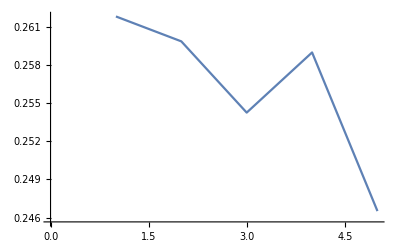

```mathematica
{0.26180217442687825,0.25984559656451195,0.2542454791879412,0.2589734554218829,0.24650619806614418}//ListLinePlot
```

```mathematica
Table[Print[x];ggg[x],{x,Range[4,20,4]}]
```

4

$Aborted

```mathematica
Clear[transmission]
```

```mathematica
transmission:=transmission=Table[{x,Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/diagonal_"<>ToString[x]<>"_ϵ1.dat"]},{x,Range[6,20,2]}]
```

```mathematica
Dimensions[transmission[[2,2]]]
```

{201,2}

```mathematica
transmission1:=transmission1=Table[Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_1_size_5050epsi1/diagonal/40imp/diagonal_"<>ToString[x]<>"_ϵ1.dat"],{x,Range[4,20,4]}]
```

```mathematica
Range[6,20,4]
```

{6,10,14,18}

```mathematica
Table[Table[Print[x];ggg[m,x],{x,Range[5,m/2,5]}],{m,Range[10,50,10]}]
```

{{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/10imp/diagonal_5_ϵ1.dat},{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/20imp/diagonal_5_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/20imp/diagonal_10_ϵ1.dat},{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/30imp/diagonal_5_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/30imp/diagonal_10_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/30imp/diagonal_15_ϵ1.dat},{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/40imp/diagonal_5_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/40imp/diagonal_10_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/40imp/diagonal_15_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/40imp/diagonal_20_ϵ1.dat},{/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/50imp/diagonal_5_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/50imp/diagonal_10_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/50imp/diagonal_15_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/50imp/diagonal_20_ϵ1.dat,/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/diagonal/lead_10_size_5050epsi1/50imp/diagonal_25_ϵ1.dat}}

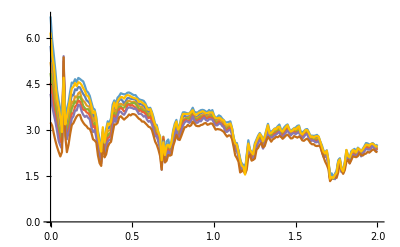

```mathematica
ListLinePlot[Import["/home/shardulmukim/PhD/fwi/sq_lattice/sudo_Q/new_data/top4th/lead_10_size_5050epsi1/diagonal/40imp/*.dat"]]
```

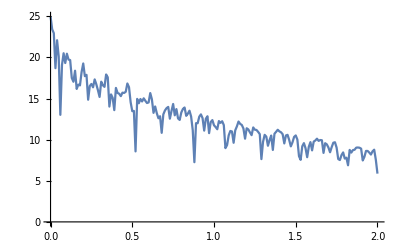

```mathematica
ListLinePlot[Table[{ω,CA[ω,0,10,10,1]},{ω,Range[0,2,0.01]}]]
```

```mathematica
({{1, 0, 1, 0}, {0, 1, 0, 1}, {1, 1, 0, 0}, {0, 0, 1, 1}})
```

{{1,0,1,0},{0,1,0,1},{1,1,0,0},{0,0,1,1}}

```mathematica
Det[{{1,0,1,0},{0,1,0,1},{1,1,0,0},{0,0,1,1}}]
```

0

```mathematica
misfit[x_,y_,n_]:=Module[{m5=input[[n]]},
ρ1=Table[{transmission[[con,1]],Module[{B1=Transpose[{m5[[1;;201]][[;;,1]],(m5[[1;;201,2]]-transmission[[con,2]][[1;;201,;;]][[;;,2]])^2}]},NIntegrate[Interpolation[B1][ω],{ω,y,x}]/((x-y)*100)]},{con,4}];lista=ρ1(*,ρ2,ρ3,ρ4*)(*,ρ5,ρ6*);
{lista,lista[[Position[lista,Min[lista]][[1,1]]]]}]
```

```mathematica
Table[misfit[2,0,n][[2]][[1]],{n,10}]
```

{12,12,12,12,12,12,12,12,12,12}

```mathematica
Tally[%216]
```

{{8,22},{12,28},{16,29},{4,21}}

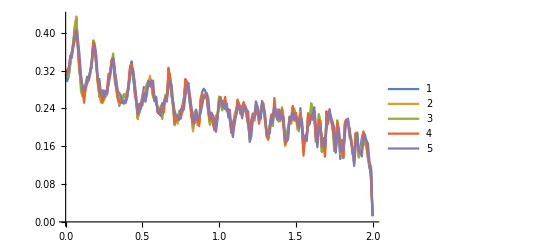

```mathematica
ListLinePlot[transmission1,PlotLegends->Placed[Automatic,Above]]
```

```mathematica
Manipulate[{n,misfit[0.65,0.1,n][[2]],Show[ListLinePlot[input[[n]]],ListLinePlot[transmission1]],Show[ListPlot[dist[12][[n]]],ListLinePlot[Table[{x,25},{x,0,50}],PlotStyle->Red],ListLinePlot[Table[{25,x},{x,0,50}],PlotStyle->Red],ListLinePlot[Table[{x,12},{x,0,50}],PlotStyle->Red]]},{n,100}]
```

Part::partw: Part 100 of {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}} does not exist.

Part::take: Cannot take positions 1 through 201 in {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}}⟦100⟧.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umn: Interpolation on unstructured grids is currently only supported for machine numbers.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umn: Interpolation on unstructured grids is currently only supported for machine numbers.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

General::stop: Further output of Interpolation::udeg will be suppressed during this calculation.

Interpolation::umn: Interpolation on unstructured grids is currently only supported for machine numbers.

General::stop: Further output of Interpolation::umn will be suppressed during this calculation.

NIntegrate::inumr: The integrand Interpolation[{{{0., 1.97153}, Power[-6.70707 + {{{0., 1.97153}, {0.01, 0.246065}, {0.02, 2.22145}, <<196>>, {1.99, 1.99913}, {2., 1.83553}}, <<9>>}[[100]][[1 ;; 201,2]], 2]}, <<199>>, {<<2>>}}][ω] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.1,0.65}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 201 in {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}}⟦100⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 100 of {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}}⟦100⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[«1»],].

Part::partw: Part 100 of {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}} does not exist.

Part::take: Cannot take positions 1 through 201 in {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}}⟦100⟧.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umn: Interpolation on unstructured grids is currently only supported for machine numbers.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

Interpolation::umn: Interpolation on unstructured grids is currently only supported for machine numbers.

Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

General::stop: Further output of Interpolation::udeg will be suppressed during this calculation.

Interpolation::umn: Interpolation on unstructured grids is currently only supported for machine numbers.

General::stop: Further output of Interpolation::umn will be suppressed during this calculation.

NIntegrate::inumr: The integrand Interpolation[{{{0., 1.97153}, Power[-6.70707 + {{{0., 1.97153}, {0.01, 0.246065}, {0.02, 2.22145}, <<196>>, {1.99, 1.99913}, {2., 1.83553}}, <<9>>}[[100]][[1 ;; 201,2]], 2]}, <<199>>, {<<2>>}}][ω] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0.1,0.65}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

Part::take: Cannot take positions 1 through 201 in {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}}⟦100⟧.

General::stop: Further output of Part::take will be suppressed during this calculation.

Part::partw: Part 1 of {} does not exist.

Part::pkspec1: The expression {}⟦1,1⟧ cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

Part::partw: Part 100 of {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}} does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListLinePlot::lpn: {{{0.,1.97153},{0.01,0.246065},{0.02,2.22145},{0.03,0.598512},{0.04,1.03859},{0.05,2.20709},{0.06,1.89963},{0.07,4.68958},{0.08,6.3866},{0.09,2.91283},{0.1,1.68309},{0.11,0.547426},{0.12,0.773144},{0.13,1.21225},{0.14,0.484983},«21»,{0.36,1.2981},{0.37,0.250913},{0.38,2.15372},{0.39,2.41828},{0.4,1.48117},{0.41,1.48444},{0.42,0.516835},{0.43,1.93309},{0.44,1.81249},{0.45,2.30599},{0.46,1.02501},{0.47,0.836343},{0.48,1.39738},{0.49,2.60033},«151»},«8»,{«1»}}⟦100⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[«1»],].

Part::partd: Part specification input⟦100⟧ is longer than depth of object.

Part::pkspec1: The expression False cannot be used as a part specification.

Part::pkspec1: The expression 100 cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

ListLinePlot::lpn: input⟦100⟧ is not a list of numbers or pairs of numbers.

ListLinePlot::lpn: transmission1 is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListLinePlot[input⟦100⟧],ListLinePlot[transmission1]].

Part::partw: Part 100 of dist[12] does not exist.

Part::partw: Part 100 of dist[12.] does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

ListPlot::lpn: dist[12.]⟦100⟧ is not a list of numbers or pairs of numbers.

Show::gcomb: Could not combine the graphics objects in Show[ListPlot[dist[12]⟦100⟧],,,].

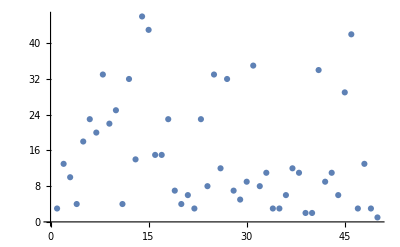

```mathematica
ListPlot[dist[10][[1]]]
```